```mathematica
<<PlotLegends`
data=Import["~/univ/bsp-cg/out-cg-mats-timing-run/data.csv","CSV"];
```

```mathematica
data[[1]]
```

{1,10000,110152,0.347325,11,1}

```mathematica
withdensity=Table[Append[data[[n]][[{1,4}]],data[[n]][[3]]], {n,1,Length[data]}];
```

```mathematica
withdensity[[4]]  (* procs, time, nz *)
```

{2,0.252093,110152}

```mathematica
sortedByDensity=Sort[withdensity,#1[[3]]< #2[[3]] &];
```

```mathematica
groupedByDensity=Gather[sortedByDensity, #1[[3]]==#2[[3]]&];
```

```mathematica
averagedByDensity=Table[Mean/@Gather[groupedByDensity[[n]],#1[[1]]==#2[[1]]&],{n,1,Length[groupedByDensity]}];
averagedByDensity=Table[Table[averagedByDensity[[n]][[m]],{m,1,Length[averagedByDensity[[n]]]}],{n,1,Length[averagedByDensity]}]
```

{{{8,0.015221,2000},{4,0.015368,2000},{2,0.019729,2000},{1,0.033563,2000}},{{8,0.0226655,5966},{4,0.0268375,5966},{2,0.043384,5966},{1,0.066748,5966}},{{8,0.0150785,6032},{4,0.0157305,6032},{2,0.0213715,6032},{1,0.0288065,6032}},{{8,0.015204,11044},{4,0.015135,11044},{2,0.0202435,11044},{1,0.026739,11044}},{{8,0.024893,22030},{4,0.0290795,22030},{2,0.042985,22030},{1,0.0583955,22030}},{{8,0.0561155,29914},{4,0.082226,29914},{2,0.134433,29914},{1,0.194671,29914}},{{8,0.025862,42228},{4,0.031051,42228},{2,0.043261,42228},{1,0.0617655,42228}},{{8,0.107927,110152},{4,0.151873,110152},{2,0.247571,110152},{1,0.348233,110152}},{{8,0.0574175,130212},{4,0.078218,130212},{2,0.118382,130212},{1,0.173033,130212}},{{8,0.0539725,256504},{4,0.066723,256504},{2,0.109247,256504},{1,0.178599,256504}},{{8,0.184517,420412},{4,0.266886,420412},{2,0.417858,420412},{1,0.626728,420412}},{{8,0.104376,511034},{4,0.143247,511034},{2,0.214019,511034},{1,0.362257,511034}},{{8,0.114722,1015308},{4,0.168289,1015308},{2,0.287841,1015308},{1,0.452878,1015308}},{{8,0.193877,2024134},{4,0.307816,2024134},{2,0.50097,2024134},{1,0.842107,2024134}},{{8,0.240949,4041652},{4,0.415712,4041652},{2,0.679868,4041652},{1,1.20559,4041652}},{{8,0.349206,10536950},{4,0.649009,10536950},{2,1.15512,10536950},{1,2.087,10536950}},{{8,0.448815,16668124},{4,0.80842,16668124},{2,1.48777,16668124},{1,2.92429,16668124}}}

```mathematica
sortByProc=(Sort[#1,(#1[[1]]<#2[[1]]&)]&)/@averagedByDensity;
sortByProc[[1]]
legend=Table[sortByProc[[n]][[1]][[3]]//N,{n,1,Length[sortByProc]}]
```

{{1,0.033563,2000},{2,0.019729,2000},{4,0.015368,2000},{8,0.015221,2000}}

{2000.,5966.,6032.,11044.,22030.,29914.,42228.,110152.,130212.,256504.,420412.,511034.,1.01531×10^6,2.02413×10^6,4.04165×10^6,1.0537×10^7,1.66681×10^7}

```mathematica
averagedByDensity=Map[(Drop[#1,-1]&),#1]&/@averagedByDensity
```

{{{8,0.015221},{4,0.015368},{2,0.019729},{1,0.033563}},{{8,0.0226655},{4,0.0268375},{2,0.043384},{1,0.066748}},{{8,0.0150785},{4,0.0157305},{2,0.0213715},{1,0.0288065}},{{8,0.015204},{4,0.015135},{2,0.0202435},{1,0.026739}},{{8,0.024893},{4,0.0290795},{2,0.042985},{1,0.0583955}},{{8,0.0561155},{4,0.082226},{2,0.134433},{1,0.194671}},{{8,0.025862},{4,0.031051},{2,0.043261},{1,0.0617655}},{{8,0.107927},{4,0.151873},{2,0.247571},{1,0.348233}},{{8,0.0574175},{4,0.078218},{2,0.118382},{1,0.173033}},{{8,0.0539725},{4,0.066723},{2,0.109247},{1,0.178599}},{{8,0.184517},{4,0.266886},{2,0.417858},{1,0.626728}},{{8,0.104376},{4,0.143247},{2,0.214019},{1,0.362257}},{{8,0.114722},{4,0.168289},{2,0.287841},{1,0.452878}},{{8,0.193877},{4,0.307816},{2,0.50097},{1,0.842107}},{{8,0.240949},{4,0.415712},{2,0.679868},{1,1.20559}},{{8,0.349206},{4,0.649009},{2,1.15512},{1,2.087}},{{8,0.448815},{4,0.80842},{2,1.48777},{1,2.92429}}}

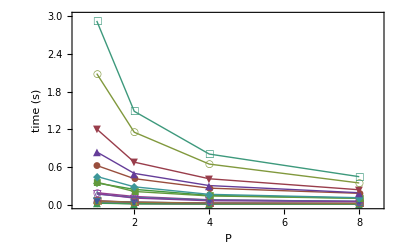

```mathematica
timerun=ListPlot[averagedByDensity,PlotRange->{{0.5,8.5},{0,3}},Joined->True,Mesh->All,FrameLabel->{{"time (s)",""},{"P",""}},PlotLegend->legend,LegendPosition->{0.7,-1},LegendSize->{1,2},PlotMarkers->Automatic,Frame->True,FrameStyle->{{Black,White},{Black,White}}]
```

```mathematica
Export["~/univ/bsp-cg/doc/img/time-run.pdf", timerun]
```

~/univ/bsp-cg/doc/img/time-run.pdf

```mathematica
speedup=Map[({#1[[1]],1/#1[[2]]})&,sortByProc,{2}]
```

{{{1,29.7947},{2,50.6868},{4,65.0703},{8,65.6987}},{{1,14.9817},{2,23.05},{4,37.2613},{8,44.1199}},{{1,34.7144},{2,46.7913},{4,63.5708},{8,66.3196}},{{1,37.3986},{2,49.3986},{4,66.072},{8,65.7722}},{{1,17.1246},{2,23.2639},{4,34.3885},{8,40.1719}},{{1,5.13687},{2,7.43865},{4,12.1616},{8,17.8204}},{{1,16.1903},{2,23.1155},{4,32.2051},{8,38.6668}},{{1,2.87164},{2,4.03925},{4,6.58445},{8,9.26556}},{{1,5.77926},{2,8.44727},{4,12.7848},{8,17.4163}},{{1,5.59915},{2,9.15361},{4,14.9873},{8,18.528}},{{1,1.59559},{2,2.39316},{4,3.74693},{8,5.41955}},{{1,2.76047},{2,4.67247},{4,6.98095},{8,9.58079}},{{1,2.2081},{2,3.47414},{4,5.94218},{8,8.71676}},{{1,1.1875},{2,1.99613},{4,3.24869},{8,5.15792}},{{1,0.829473},{2,1.47087},{4,2.40551},{8,4.15026}},{{1,0.479156},{2,0.865715},{4,1.54081},{8,2.86364}},{{1,0.341963},{2,0.672146},{4,1.23698},{8,2.22809}}}

```mathematica
For[j=1,j<=Length[speedup],j++,For[i=2,i<=Length[speedup[[j]]],i++,speedup[[j]][[i]][[2]]=speedup[[j]][[i]][[2]]/speedup[[j]][[1]][[2]]]
]
For[j=1,j<=Length[speedup],j++,speedup[[j]][[1]][[2]]=1
]
```

```mathematica
speedup
```

{{{1,1},{2,1.7012},{4,2.18395},{8,2.20505}},{{1,1},{2,1.53854},{4,2.48712},{8,2.94492}},{{1,1},{2,1.34789},{4,1.83125},{8,1.91044}},{{1,1},{2,1.32087},{4,1.7667},{8,1.75868}},{{1,1},{2,1.35851},{4,2.00813},{8,2.34586}},{{1,1},{2,1.44809},{4,2.36751},{8,3.46911}},{{1,1},{2,1.42774},{4,1.98916},{8,2.38827}},{{1,1},{2,1.4066},{4,2.29292},{8,3.22658}},{{1,1},{2,1.46165},{4,2.21218},{8,3.01358}},{{1,1},{2,1.63482},{4,2.67672},{8,3.30906}},{{1,1},{2,1.49986},{4,2.3483},{8,3.39658}},{{1,1},{2,1.69264},{4,2.5289},{8,3.47071}},{{1,1},{2,1.57336},{4,2.69108},{8,3.94763}},{{1,1},{2,1.68095},{4,2.73575},{8,4.34352}},{{1,1},{2,1.77326},{4,2.90005},{8,5.0035}},{{1,1},{2,1.80675},{4,3.21568},{8,5.97642}},{{1,1},{2,1.96555},{4,3.61729},{8,6.51558}}}

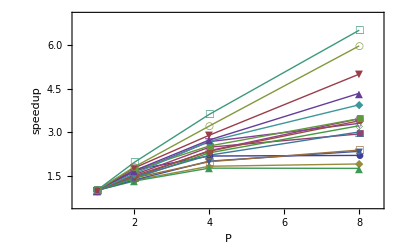

```mathematica
speedupplot=ListPlot[speedup,Joined->True,Mesh->All,PlotRange->{{.5,8.5},{.5,7}},FrameLabel->{{"speedup",""},{"P",""}},PlotLegend->legend,LegendPosition->{0.7,-1},LegendSize->{1,2},PlotMarkers->Automatic,Frame->True,FrameStyle->{{Black,White},{Black,White}}]
```

```mathematica
Export["~/univ/bsp-cg/doc/img/speedup.pdf", speedupplot]
```

~/univ/bsp-cg/doc/img/speedup.pdf